```mathematica
Quit[]
```

### Computing the Numerical profile

```mathematica
Dgg=gg'[r]==(-2 c Mp w^2 gg[r]^5 ϕ[r]^2 (w^2 gg[r]^2 ϕ[r]^2-NN[r]^2 ϕ'[r]^2)^2-2 c Mp gg[r]^3 (w^2 gg[r]^2 ϕ[r]^2-NN[r]^2 ϕ'[r]^2)^2 (-w^2 ϕ[r]^2+NN[r]^2 ϕ'[r]^2)+Λ^3 gg[r]^3 (r^2 w^2 ϕ[r]^2+NN[r]^2 (-Mp^2+m^2 r^2 ϕ[r]^2)) (w^2 gg[r]^3 ϕ[r]^2-gg[r] NN[r]^2 ϕ'[r]^2)^2+Λ^3 gg[r] NN[r]^2 (Mp^2+r^2 ϕ'[r]^2) (w^2 gg[r]^3 ϕ[r]^2-gg[r] NN[r]^2 ϕ'[r]^2)^2-2 d Mp gg[r] NN[r]^6 ϕ'[r]^5 (ϕ'[r]+4 r ϕ''[r])-2 c Mp gg[r] NN[r]^2 ϕ'[r] (w^2 gg[r]^2 ϕ[r]^2-NN[r]^2 ϕ'[r]^2)^2 (ϕ'[r]+4 r ϕ''[r])-4 d Mp r w^2 gg[r]^3 NN[r]^4 ϕ[r] ϕ'[r]^3 (3 ϕ'[r]^2-5 ϕ[r] ϕ''[r])+2 d Mp w^4 gg[r]^5 NN[r]^2 ϕ[r]^3 ϕ'[r] (-2 r ϕ'[r]^2+ϕ[r] (ϕ'[r]+2 r ϕ''[r])))/(4 d Mp r w^4 gg[r]^4 NN[r]^2 ϕ[r]^4 ϕ'[r]^2+24 d Mp r w^2 gg[r]^2 NN[r]^4 ϕ[r]^2 ϕ'[r]^4-12 d Mp r NN[r]^6 ϕ'[r]^6+4 c Mp r w^2 gg[r]^2 ϕ[r]^2 (w^2 gg[r]^2 ϕ[r]^2-NN[r]^2 ϕ'[r]^2)^2-12 c Mp r NN[r]^2 ϕ'[r]^2 (w^2 gg[r]^2 ϕ[r]^2-NN[r]^2 ϕ'[r]^2)^2+2 Λ^3 Mp^2 r NN[r]^2 (w^2 gg[r]^3 ϕ[r]^2-gg[r] NN[r]^2 ϕ'[r]^2)^2);

DNN=NN'[r]==(NN[r] (w^2 gg[r]^2 ϕ[r]^2-NN[r]^2 ϕ'[r]^2) (w^2 gg[r]^6 ϕ[r]^2 ((-2 c Mp+Λ^3 r^2) w^2 ϕ[r]^2+Λ^3 NN[r]^2 (Mp-m r ϕ[r]) (Mp+m r ϕ[r]))-6 (c+d) Mp NN[r]^4 ϕ'[r]^4+gg[r]^4 (-Λ^3 Mp^2 w^2 NN[r]^2 ϕ[r]^2+Λ^3 NN[r]^4 (-Mp^2+m^2 r^2 ϕ[r]^2) ϕ'[r]^2+2 c Mp w^4 ϕ[r]^3 (ϕ[r]+4 r ϕ'[r]))+gg[r]^2 NN[r]^2 ϕ'[r] (NN[r]^2 ϕ'[r] (Λ^3 Mp^2+(2 c Mp-Λ^3 r^2) ϕ'[r]^2)+2 Mp w^2 ϕ[r] (ϕ'[r] ((2 c+d) ϕ[r]-2 (2 c+3 d) r ϕ'[r])+2 d r ϕ[r] ϕ''[r]))))/(2 Mp r (gg[r]^6 (Λ^3 Mp w^4 NN[r]^2 ϕ[r]^4+2 c w^6 ϕ[r]^6)-2 w^2 gg[r]^4 NN[r]^2 ϕ[r]^2 (Λ^3 Mp NN[r]^2+(5 c-d) w^2 ϕ[r]^2) ϕ'[r]^2+gg[r]^2 NN[r]^4 (Λ^3 Mp NN[r]^2+2 (7 c+6 d) w^2 ϕ[r]^2) ϕ'[r]^4-6 (c+d) NN[r]^6 ϕ'[r]^6));

DDPhi=ϕ''[r]==(w^6 gg[r]^11 ((-2 c Mp+Λ^3 r^2) w^2-Λ^3 m^2 r^2 NN[r]^2) ϕ[r]^7+6 (c+d) Mp NN[r]^7 gg'[r] (NN[r]+2 r NN'[r]) ϕ'[r]^7-w^6 gg[r]^8 ϕ[r]^6 gg'[r] (4 c Mp r w^2 ϕ[r]+(-2 c Mp+Λ^3 r^2) NN[r]^2 ϕ'[r])+w^4 gg[r]^9 ϕ[r]^5 (2 c Mp w^4 ϕ[r]^2+w^2 NN[r] ϕ[r] (2 Λ^3 r NN[r]+(-2 c Mp+Λ^3 r^2) NN'[r]) ϕ'[r]+3 NN[r]^2 ((2 c Mp-Λ^3 r^2) w^2+Λ^3 m^2 r^2 NN[r]^2) ϕ'[r]^2)+w^2 gg[r]^4 NN[r]^3 ϕ[r]^2 ϕ'[r]^3 (4 (9 c+13 d) Mp r w^2 ϕ[r]^2 gg'[r] NN'[r]+3 (2 c Mp-Λ^3 r^2) NN[r]^3 gg'[r] ϕ'[r]^2+2 Mp w^2 NN[r] ϕ[r] (-2 (3 c+8 d) r gg'[r] ϕ'[r]+ϕ[r] (3 (3 c+d) gg'[r]-2 d r gg''[r])))+gg[r]^2 NN[r]^5 ϕ'[r]^5 (-4 (9 c+10 d) Mp r w^2 ϕ[r]^2 gg'[r] NN'[r]+(-2 c Mp+Λ^3 r^2) NN[r]^3 gg'[r] ϕ'[r]^2-2 Mp w^2 NN[r] ϕ[r] (-(2 c+7 d) r gg'[r] ϕ'[r]+ϕ[r] ((9 c+7 d) gg'[r]-d r gg''[r])))+w^4 gg[r]^6 NN[r] ϕ[r]^4 ϕ'[r] (4 (-3 c+2 d) Mp r w^2 ϕ[r]^2 gg'[r] NN'[r]+3 (-2 c Mp+Λ^3 r^2) NN[r]^3 gg'[r] ϕ'[r]^2+2 Mp w^2 NN[r] ϕ[r] (3 (2 c+3 d) r gg'[r] ϕ'[r]+ϕ[r] ((-3 c+d) gg'[r]+d r gg''[r])))-2 Mp gg[r] NN[r]^6 ϕ'[r]^5 (2 d r w^2 ϕ[r]^2 gg'[r]^2+(c+d) NN[r] ϕ'[r]^2 (3 NN'[r]+2 r NN''[r]))-w^2 gg[r]^7 NN[r] ϕ[r]^3 ϕ'[r] (6 Mp w^4 ϕ[r]^2 ((c+d) NN[r]+d r NN'[r]) ϕ'[r]+w^2 NN[r] ϕ[r] (-4 d Mp r w^2+6 Λ^3 r NN[r]^2+3 (-2 c Mp+Λ^3 r^2) NN[r] NN'[r]) ϕ'[r]^2+3 NN[r]^3 ((2 c Mp-Λ^3 r^2) w^2+Λ^3 m^2 r^2 NN[r]^2) ϕ'[r]^3+2 Mp w^4 ϕ[r]^3 ((-3 c+d) NN'[r]+(-2 c+d) r NN''[r]))+gg[r]^5 NN[r]^2 ϕ[r] ϕ'[r] (-8 d Mp r w^6 ϕ[r]^5 gg'[r]^2+2 Mp w^4 NN[r] ϕ[r]^2 ((3 c+8 d) NN[r]+12 d r NN'[r]) ϕ'[r]^3+3 w^2 NN[r]^3 ϕ[r] (2 Λ^3 r NN[r]+(-2 c Mp+Λ^3 r^2) NN'[r]) ϕ'[r]^4+NN[r]^4 ((2 c Mp-Λ^3 r^2) w^2+Λ^3 m^2 r^2 NN[r]^2) ϕ'[r]^5-2 Mp w^4 ϕ[r]^3 ϕ'[r]^2 (14 d r NN'[r]^2+NN[r] ((9 c+7 d) NN'[r]+2 (3 c+2 d) r NN''[r])))+gg[r]^3 NN[r]^4 ϕ'[r]^3 (12 d Mp r w^4 ϕ[r]^4 gg'[r]^2-2 Mp w^2 NN[r] ϕ[r] ((c+5 d) NN[r]-7 d r NN'[r]) ϕ'[r]^3-NN[r]^2 (4 d Mp r w^2+2 Λ^3 r NN[r]^2+(-2 c Mp+Λ^3 r^2) NN[r] NN'[r]) ϕ'[r]^4+2 Mp w^2 ϕ[r]^2 ϕ'[r]^2 (-2 d r NN'[r]^2+NN[r] ((9 c+11 d) NN'[r]+(6 c+7 d) r NN''[r]))))/(gg[r] NN[r] ((2 c Mp-Λ^3 r^2) w^6 gg[r]^8 NN[r] ϕ[r]^6-2 d Mp r w^6 gg[r]^5 NN[r] ϕ[r]^6 gg'[r]+2 d Mp r w^2 gg[r] NN[r]^5 ϕ[r]^2 gg'[r] ϕ'[r]^4+2 (c+d) Mp NN[r]^6 (NN[r]+2 r NN'[r]) ϕ'[r]^6+w^2 gg[r]^4 NN[r]^2 ϕ[r]^2 ϕ'[r]^2 (12 (c+3 d) Mp r w^2 ϕ[r]^2 NN'[r]+3 (2 c Mp-Λ^3 r^2) NN[r]^3 ϕ'[r]^2+2 Mp w^2 NN[r] ϕ[r] (3 (c+d) ϕ[r]-8 d r ϕ'[r]))+w^4 gg[r]^6 ϕ[r]^4 (2 (-2 c+d) Mp r w^2 ϕ[r]^2 NN'[r]+3 (-2 c Mp+Λ^3 r^2) NN[r]^3 ϕ'[r]^2-2 Mp w^2 NN[r] ϕ[r] (c ϕ[r]-6 d r ϕ'[r]))-gg[r]^2 NN[r]^4 ϕ'[r]^4 (2 (6 c+5 d) Mp r w^2 ϕ[r]^2 NN'[r]+(2 c Mp-Λ^3 r^2) NN[r]^3 ϕ'[r]^2+2 Mp w^2 NN[r] ϕ[r] (3 c ϕ[r]+4 d ϕ[r]-2 d r ϕ'[r]))));
```

```mathematica
SeidelEqsList={};
SeidelEqsListH={};
SeidelBCList={};
SeidelBCListH={};
SeidelCoefFunctionsList={};
AppendTo[SeidelEqsList,{DDPhi,DNN,Dgg}];

AppendTo[SeidelCoefFunctionsList,{NN,gg,φ}];

AppendTo[SeidelBCList,{NN[rMin]==N0,gg[rMin]==1.,φ[rMin]==ϕ0, φ'[rMin] == 0,NN'[rMin] ==0, gg'[rMin] == 0}];
```

```mathematica
SeidelBCList
```

{{NN[rMin]==N0,gg[rMin]==1.,φ[rMin]==ϕ0,φ'[rMin]==0,NN'[rMin]==0,gg'[rMin]==0}}

#### Test

```mathematica
m2BH={{0.01,1.036914,40,30,-2,10^-8},{0.011,1.04112,35,30,-2,10^-8},{0.012,1.045424,35,30,-2,10^-8},{0.014,1.05434,30,30,-2,10^-8},{0.015,1.0592,22,30,-2,10^-8},{0.02,1.083925816044137550,21},{0.03,1.143860134940767460,16},{0.04,1.222191189880697980,11.75}};
```

```mathematica
{0.035,1.1469744359479111622314453124999999999977394486026723486766`30.,17,30,-0.3,10^-8}
```

```mathematica
η=0.3;
c4=1/2;d4=2*c4;
L3=(1/η)^(1/3);
Mp=1;mS=1;N0=1;
rMin=10^-8;
rMax=17;
ϕ0=0.035*√(8π);
 w=1.1469744359479111(*1.220956134940767460, r=15 *)

s1=NDSolve[{SeidelEqsList[[1]],SeidelBCList[[1]]},SeidelCoefFunctionsList[[1]],{r,rMin,rMax},Method->{"EquationSimplification"->"Residual"}]
```

1.14697

{{NN→InterpolatingFunction[…],gg→InterpolatingFunction[…],φ→InterpolatingFunction[…]}}

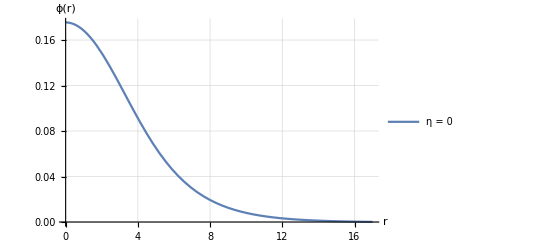

```mathematica
Plot[{Evaluate[φ[r]/.s1]},{r,rMin,rMax},
Background->White,PlotLegends->Placed[{"η = 0"(*, "η = 0.01","η = 0.1"*), "η = 0.5","η = 0.95"(*, "η = -0.01","η = -0.1"*), "η = -0.5","η = -0.95"},{0.85,0.65}],
PlotRange->Full,AxesLabel->{"r","ϕ(r)"},
GridLines->Automatic,AxesOrigin->{0,0}]
```

```mathematica
M[r_]:=Evaluate[1/2 r (1-1/gg[r]^2)/.s1]8π; 
M[rMax]
```

{21.7582}

```mathematica
M95=Last[M[rMax]]*0.95
```

31.1946

```mathematica
r95=FindRoot[M[r]==M95,{r,rMin,rMax}][[1,2]]
```

7.85084

```mathematica
M[rMax]/r95
```

{4.18253}

```mathematica
B=NumberForm[Solve[C*Evaluate[NN[rMax]/.s1]*Evaluate[gg[rMax]/.s1]==1,C],{18,17}];
w2=w*B[[1,1,1,2]]
```

0.906225

```mathematica
(* Solving again *)
SeidelBCList={};
Clear[ w,N0];

AppendTo[SeidelBCList,{NN[rMin]==N0,gg[rMin]==1.,φ[rMin]==ϕ0, φ'[rMin] == 0,NN'[rMin] ==0, gg'[rMin] == 0}];

N0= B[[1,1,1,2]];
w=w2;(*0.7799069890227248*)
Print[w];
```

0.906225

```mathematica
w=0.9062353622499302;
rMax=21
s1=NDSolve[{SeidelEqsList[[1]],SeidelBCList[[1]]},SeidelCoefFunctionsList[[1]],{r,rMin,rMax},Method->{"EquationSimplification"->"Residual"}]
```

21

{{NN→InterpolatingFunction[…],gg→InterpolatingFunction[…],φ→InterpolatingFunction[…]}}

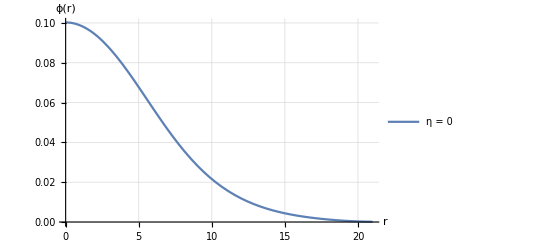

```mathematica
Plot[{Evaluate[φ[r]/.s1]},{r,rMin,rMax},
Background->White,PlotLegends->Placed[{"η = 0"(*, "η = 0.01","η = 0.1"*), "η = 0.5","η = 0.95"(*, "η = -0.01","η = -0.1"*), "η = -0.5","η = -0.95"},{0.85,0.65}],
PlotRange->Full,AxesLabel->{"r","ϕ(r)"},
GridLines->Automatic,AxesOrigin->{0,0}]
```

```mathematica
isco[r_]:=Evaluate[NN[r]-r NN'[r]/.s1]
```

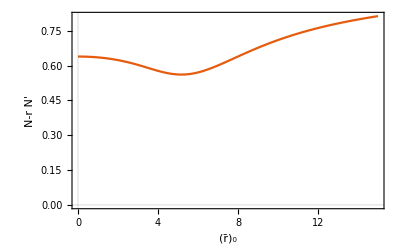

```mathematica
Plot[isco[r],{r,rMin,rMax},AxesOrigin->{0,0},PlotTheme->"Scientific",FrameLabel->{"(r̄)_0","N-r N'"},ImageSize->400]
```

### data

```mathematica
Etam03={{0.001,1.00327793625,200,30, -0.3,10^-6},{0.005,1.016833476,50,30, -0.3,10^-8},{0.007,1.02388729657578,40,30,-0.3,10^-8},
{0.008,1.0274865425,40,30,-0.3,10^-6},{0.01,1.03483418567889,40.0,30,-0.3,10^-6},{0.012,1.04239623,30,30,-0.3,10^-8},
{0.015,1.054140552042320860,28,30,-0.3,10^-8},{0.02,1.074838765,28,30,-0.3,10^-8},{0.025,1.097106,28,30,-0.3,10^-8},
{0.028,1.1112783,28,30,-0.3,10^-8},{0.03,1.121086874,28,30,-0.3,10^-8},{0.04,1.1748856363351694,20,30,-0.3,10^-8},
{0.042,1.186707863351694,20,30,-0.3,10^-8},{0.044,1.198901393441151350,20,30,-0.3,10^-8},{0.046,1.211505343101943020,20,30,-0.3,10^-8},
{0.048,1.224518674759,20,30,-0.3,10^-8},{0.05,1.23797072572627,20,30,-0.3,10^-8},{0.052,1.25187767561304990,20,30,-0.3,10^-8},
{0.054,1.26625468873317999,20,30,-0.3,10^-8},{0.056,1.281110391763441167405,18,30,-0.3,10^-8},{0.058,1.29647849577,16,30,-0.3,10^-8},
{0.06,1.3124032435360,16,30,-0.3,10^-8},{0.07,1.4008143125450540,16,30,-0.3,10^-8},{0.08,1.5063484517423,12,30,-0.3,10^-8},{0.09,1.633272745017423,12,30,-0.3,10^-8}};
```

```mathematica
Eta03={{0.0001,1.0003256998,500,30,0.3,10^-6},{0.0003,1.000978223655,500,30,0.3,10^-5},{0.0005,1.0016317435,300,30,0.3,10^-6},{0.0007,1.00228644,200,30,0.3,10^-6},{0.0009,1.002942285,200,30,0.3,10^-6},{0.001,1.003270638,200,30,0.3,10^-6},{0.0013,1.00425742,200,30,0.3,10^-6},(*{0.0015,1.00491662,150,30,0.3,10^-6},*){0.0017,1.0055770939968,140,30,0.3,10^-6},
{0.0019,1.006238575,140,30,0.3,10^-6},{0.003,1.009897474,140,30,0.3,10^-5},{0.005,1.0166384235237,80,30,0.3,10^-5},
{0.006,1.02005146416,60,30,0.3,10^-5},{0.0065,1.0217684,60,30,0.3,10^-5},{0.0067,1.0224568,60,30,0.3,10^-5},
{0.00673,1.02256,60,30,0.3,10^-5},{0.00675,1.0226293,60,30,0.3,10^-5},{0.00678,1.0227326,60,30,0.3,10^-5},
{0.0068,1.02280181,60,30,0.3,10^-5},{0.0069,1.0231467,60,30,0.3,10^-5},{0.007,1.02349218,60,30,0.3,10^-5},
{0.0072,1.02418,40,30,0.3,0.4*10^-5},{0.0074,1.02487,40,30,0.3,0.4*10^-5},{0.0076,1.02556,40,30,0.3,10^-5},
 {0.0078,1.02626,40,30,0.3,0.4*10^-5},{0.008,1.02695,40,30,0.3,0.4*10^-5},{0.0086,1.02905,40,30,0.3,0.4*10^-5},{0.0088,1.029753,40,30,0.3,0.4*10^-5},{0.009,1.03045,40,30,0.3,0.4*10^-5},{0.0094,1.0318568,40,30,0.3,10^-5},
{0.01,1.0339767,40,30,0.3,0.4*10^-5},{0.010009,1.03401,30,30,0.3,0.4*10^-5},{0.0102,1.03467,30,30,0.3,0.4*10^-5},{0.0107,1.03644,30,30,0.3,0.4*10^-5},{0.0109,1.03721,25,30,0.3,10^-8},{0.011,1.03751,30,30,0.3,10^-8},
{0.0115,1.03932,30,30,0.3,10^-5},{0.012,1.041114,40,30,0.3,10^-5},{0.015,1.05201083,40,30,0.3,10^-6},
{0.018,1.0631343,32,30,0.3,10^-6},{0.019,1.06687854,26,30,0.3,10^-6},{0.02,1.070630178,23,30,0.3,10^-6},{0.022,1.0783017,21,30,0.3,10^-6},{0.025,1.089844,20,30,0.3,10^-6},{0.03,1.10946951,30,30,0.3,10^-8},{0.031,1.1134168,30,30,0.3,10^-8},{0.032,1.11736085,24,30,0.3,10^-8},{0.033,1.1213,20,30,0.3,10^-8},{0.034,1.12524,20,30,0.3,10^-8},{0.035,1.1291682,19,30,0.3,10^-8}};(*0.4*10^-5*)
```

```mathematica
Bs={{0.0010000000000000000208166817117216851329430937767028808594`30.,1.0032736825266425024546711200243289808219829642490431642279`30.,150,30,0,0.01`30.},{0.0020000000000000000416333634234433702658861875534057617188`30.,1.0065835949573696846177350275907531973318828825330502424441`30.,100.0700000000034,30,0,0.01`30.},
(*{0.0030000000000000000624500451351650553988292813301086425781`30.,1.0099321063764611044831211129554904282201732712564989924431`30.,60.06999999999989,30,0,0.01`30.},*){0.0032000000000000001533495552763497471460141241550445556641`30.,1.0106016081544170002223179530436890442542455237351362029585`30.,60.069999999999716,30,0,0.01`30.},{0.0035999999999999999014677065645173570374026894569396972656`30.,1.011954987515376924431307884387624283415146181352994858571`30.,60.06999999999983,30,0,0.01`30.},{0.0040000000000000000832667268468867405317723751068115234375`30.,1.0133129876708166055894180393211253105701470308974698752991`30.,60.06999999999994,30,0,0.01`30.},{0.0044000000000000002650657471292561240261420607566833496094`30.,1.0146771488855626293463551590407140550506148030107667068478`30.,60.0699999999996,30,0,0.01`30.},{0.0047999999999999995795030294232219603145495057106018066406`30.,1.0160472144488105647605014533469701953013217092525177775997`30.,60.06999999999983,30,0,0.01`30.},{0.0051999999999999997613020497055913438089191913604736328125`30.,1.0174231843605604118318569222398937313222677496227230875547`30.,60.069999999999716,30,0,0.01`30.},{0.0054666666666666665491680632271709328051656484603881835938`30.,1.018344006016054199414870367560587149924344885221216827631`30.,60.06999999999949,30,0,0.01`30.},{0.00793333333333333390324781930758035741746425628662109375`30.,1.0269905817532166681635218399975813079183506459912678110413`30.,60.06999999999966,30,0,0.01`30.},{0.010399999999999999522604099411182687617838382720947265625`30.,1.035877489321508490142804696249468742602628523741259414237`30.,60.06999999999926,30,0,0.01`30.},{0.0128666666666666668766838554915921122301369905471801757812`30.,1.0450121304801593362174921948526086434039261176265345198999`30.,60.06999999999977,30,0,0.01`30.},{0.0153333333333333324960401355951944424305111169815063476562`30.,1.0544028365789439100604072456968878003943835446661742016872`30.,50.06999999999977,30,0,0.01`30.},
{0.0177999999999999998501198916756038670428097248077392578125`30.,1.0640581996429191519093299377975697251357036014120390453319`30.,50.06999999999989,30,0,0.01`30.},
{0.02026666666666666893892312373282038606703281402587890625`30.,1.0739868036134406465836717132219519480499393153800694440886`30.,40.06999999999994,30,0,0.01`30.},{0.0227333333333333310888324518828085274435579776763916015625`30.,1.0841977627770874465590274159289713584768273016454656708576`30.,40.06999999999989,30,0,0.01`30.},{0.02520000000000000017763568394002504646778106689453125`30.,1.0947006056786406716104757733107748507119282202911661427939`30.,40.06999999999994,30,0,0.01`30.},{0.027666666666666665796991964043627376668155193328857421875`30.,1.1055050253841343332553983559482949272163299758359577149797`30.,40.06999999999994,30,0,0.01`30.},{0.03013333333333333141634824414722970686852931976318359375`30.,1.116621675308330270834470692444677922878711745038039017396`30.,40.06999999999989,30,0,0.01`30.},{0.03260000000000000397459842815806041471660137176513671875`30.,1.1280614286283593470397314504385750221800343992547902878813`30.,40.06999999999989,30,0,0.01`30.},{0.035066666666666669593954708261662744916975498199462890625`30.,1.139835246169145591954234162767783603568587105141681801049`30.,40.06999999999989,30,0,0.01`30.},{0.0375333333333333352133109883652650751173496246337890625`30.,1.1519550542739285921023498946308235325655241567194072317374`30.,40.06999999999994,30,0,0.01`30.},{0.04,1.16447077028579,20.,30.,0.,1.*^-8},{0.042,1.174863039742705,20.,30.,0.,1.*^-8},{0.044,1.185506651020017,30.,30.,0.,1.*^-8},{0.046,1.196408378494969,30.,30.,0.,1.*^-8},{0.048,1.207576510035849,20.,30.,0.,1.*^-8},{0.05,1.219018571342151,20.,30.,0.,1.*^-8},{0.052,1.230742623941348,20.,30.,0.,1.*^-8},{0.054,1.242757501645907,20.,30.,0.,1.*^-8},{0.056,1.255071652560727,20.,30.,0.,1.*^-8},{0.058,1.267694320796101,18.,30.,0.,1.*^-8},{0.06,1.28063495884173,15.,30.,0.,1.*^-8},{0.07,1.350463702269447,30.,30.,0.,1.*^-8},{0.08,1.429880054976501,23.,14.,0.,1.*^-8},{0.09,1.520545101912098,14.,30.,0.,1.*^-8},{0.1,1.624469884859628,14.,30.,0.,1.*^-8},{0.11,1.7441016166994885,20.,30.,0.,1.*^-8},{0.13,2.0430621612059983,13.,30.,0.,1.*^-8},{0.15,2.449966765699886,13.,30.,0.,1.*^-8},{0.152,2.4958022244291476,18.,30.,0.,0.01},{0.1592,2.68250370388174,20.070000000000014,30.,0.,0.01},{0.16,2.7080677018789943,19.,30.,0.,1.*^-8},{0.1664,2.892505947790201,20.070000000000014,30.,0.,0.01},{0.17,3.012458355733277,19.,30.,0.,1.*^-8},{0.1736,3.1289332343242386,20.070000000000014,30.,0.,0.01},{0.1808,3.3952169283467635,20.070000000000014,30.,0.,0.01},{0.188,3.695071314017931,20.070000000000014,30.,0.,0.01},{0.19,3.7975050018636938,14.,30.,0.,1.*^-8},{0.2,4.300155639648437,13.1,30.,0.,1.*^-8},{0.22,5.590762832128472,13.,30.,0.,1.*^-8},{0.25,8.503837558382656,14.,30.,0.,1.*^-8},{0.3,18.2904052734375,12.,30.,0.,1.*^-8}};
```

## Lensing

```mathematica
{0.2707158536601480511996945836206492728674388193275676526397`30.,15.908929743835072}
```

```mathematica
Bs[[30]]
```

{0.054,1.24276,20.,30.,0.,1.×10^-8}

```mathematica
0.175/Sqrt[8π]
```

0.0349074

```mathematica
Etam03[[23]]
```

{0.07,1.40081,16,30,-0.3,1/100000000}

```mathematica
5.047580079292602
```

```mathematica
Length[data]-2
```

#### profile

```mathematica
data={{0.054,1.242757501645907,20.,30.,0.,1.*^-8}};(*{{0.035,1.1469744359479111,17,30,-0.3,10^-8}}*);
```

```mathematica
data=Etam03;
```

```mathematica
Clear[w, s0,s1,AA,rMax,rlim,c4]
```

1

0.054

{{NN→InterpolatingFunction[…],gg→InterpolatingFunction[…],φ→InterpolatingFunction[…]}}

0.853187

19.49 20.

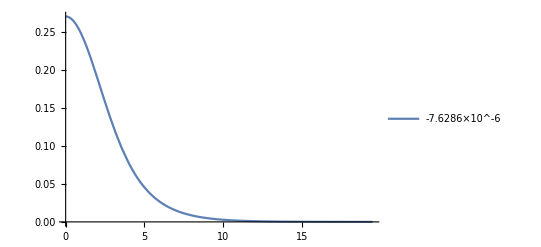

radio95 = r→6.01466

```mathematica
Do[
AA=data[[i]];

Print[i];

SeidelBCList={};
Clear[rMin,ϕ0,r,c4,α,η,L1,w,N0];

AppendTo[SeidelBCList,{NN[rMin]==N0,gg[rMin]==1.,φ[rMin]==ϕ0, φ'[rMin] == 0,NN'[rMin] ==0, gg'[rMin] == 0}];

(* Solving *)
prec=AA[[4]];
η= Abs[AA[[5]]]; 
Mp=1;mS=1;N0=1;
rMin=AA[[6]];
ϕ0=AA[[1]]*√(8π);
w=AA[[2]];
rMax=AA[[3]];
c4=0(*1/2*);
d4=0(*1*);
L3=4(*(1/η)^(1/3)*);
N0=1;
Print[AA[[1]]];

s0=NDSolve[{SeidelEqsList[[1]],SeidelBCList[[1]]},SeidelCoefFunctionsList[[1]],{r,rMin,rMax},Method->{"EquationSimplification"->"Residual"}];

Print[s0];

B=NumberForm[Solve[C*Evaluate[NN[rMax]/.s0]*Evaluate[gg[rMax]/.s0]==1,C],{18,17}];
w2=w*B[[1,1,1,2]];

(* Solving again *)
SeidelBCList={};
Clear[ w,N0];

AppendTo[SeidelBCList,{NN[rMin]==N0,gg[rMin]==1.,φ[rMin]==ϕ0, φ'[rMin] == 0,NN'[rMin] ==0, gg'[rMin] == 0}];

N0= B[[1,1,1,2]];
w=w2;(*0.76869152435647894;0.94812141164018564 w2 w=71036896476977879; Length[data]*)
Print[w];

s1=NDSolve[{SeidelEqsList[[1]],SeidelBCList[[1]]},SeidelCoefFunctionsList[[1]],{r,rMin,rMax},Method->{"EquationSimplification"->"Residual"}];

Clear[rlim, ϕ20,r0,enc];
ϕ20=ϕ0;
r0=rMin;
enc=0;
Do[
temp=ϕ20;
rtemp=r0;
If[Evaluate[φ[rB]/.s1][[1]]>temp||Evaluate[φ[rB]/.s1][[1]]<0,
(*Print[temp, "no cumplió ",Evaluate[φ[rB]/.s1][[1]]];*)
rlim=N[rtemp];
enc=1;
Break[],
ϕ20=Evaluate[φ[rB]/.s1][[1]];
r0=rB
],
{rB,rMin,rMax,0.001}];
If[enc==0,rlim=rMax];

Print[rlim, " ", rMax];

Print[
Plot[Evaluate[φ[r]/.s1],{r,rMin,rlim},PlotLegends->{Evaluate[φ[rMax]/.s1]}]
];

M[r_]:=Evaluate[1/2 r (1-1/gg[r]^2)/.s1]8π; 

M95=0.95M[rMax][[1]];

(* calculando radio *)
rad=Last[FindRoot[M[r]==M95,{r,rMin+0.5,rMax}]];
Print["radio95 = ", rad];

,{i,1,1}(*Length[data]-2*)]
```

#### lensing

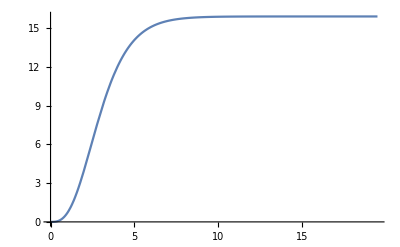

15.909

```mathematica
M[r_]:=1/2 r (1-1/gg[r]^2)8π; 

Plot[Evaluate[M[r]/.s1],{r,rMin,rlim}]
Masa=Last@Evaluate[M[rlim]/.s1]
```

```mathematica
ϕ0
```

0.175464

```mathematica
dat={};
Do[
AppendTo[dat,{i,Last@Evaluate[M[i]/.s1]}],{i,rMin,rlim,0.01}
]
```

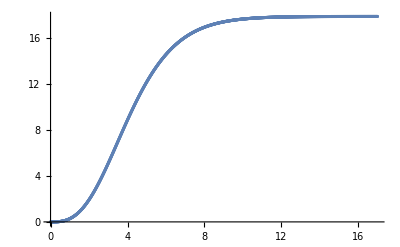

```mathematica
ListPlot[dat]
```

```mathematica
Export["M_profile_BH_L3_1_5sig0_175.dat",dat]
```

M_profile_BH_L3_1_5sig0_175.dat

```mathematica
20.13989689808094 (*BH, rho0=0.35*)
15.90897267397468(*BS, rho0=0.27*)
```

```mathematica
15.9089726739743/(8Pi)
```

0.632998

```mathematica
(*n=Sqrt[(1-(2 masa)/(8π r))]*)
```

```mathematica
(*z^2/(1/(1-(2 masa)/(8π r/z)))-(1-(2 masa)/(8π r))/(1/(1-(2 masa)/(8π r/z))(1-(2 masa)/(8π r/z)))+(1-(2 masa)/(8π r))*)
```

```mathematica
(* Definiendo el potencial *)

With[{NN=NN/.s1[[1,1]],gg=gg/.s1[[1,2]]},
VG[z_,r0_]:=Piecewise[{{z^2/gg[r0/z]^2-NN[r0]^2/(gg[r0/z]^2 NN[r0/z]^2)+NN[r0]^2,r0/z≤rlim},{z^2-Masa/(4 π r0) z^3,r0/z>rlim}}];
(*VG[z_,r0_]:=z^2/gg[r0/z]^2-NN[r0]^2/(gg[r0/z]^2 NN[r0/z]^2)+NN[r0]^2;*)
]
```

```mathematica
(* Calculando los v0 *)
```

```mathematica
vs[r0_]:=Module[{r0v=r0},

pointsZ=Subdivide[10^-3,1,200]; (* range of z values *)
(*Print["min z value", N@r0/rMax];*)

(* Generating data *)

data={};
Do[z=pointsZ[[i]];
AppendTo[data,{z,VG[z,r0v]}],{i,1,Length[pointsZ]}];

(* Fit v1,....,v6 *)
nlm=NonlinearModelFit[data,v1 x+v2 x^2+v3 x^3+v4 x^4+v5 x^5+v6 x^6+v7 x^7+v8 x^8+v9 x^9+v10 x^10+v11 x^11+v12 x^12+v13 x^13+v14 x^14+v15 x^15+v16 x^16,
{v1,v2,v3,v4,v5,v6,v7,v8,v9,v10,v11,v12,v13,v14,v15,v16},x];

modelo[x_]:=v1 x+v2 x^2+v3 x^3+v4 x^4+v5 x^5+v6 x^6+v7 x^7+v8 x^8+v9 x^9+v10 x^10+v11 x^11+v12 x^12+v13 x^13+v14x^14+v15 x^15+v16 x^16/.nlm["BestFitParameters"];

error={};
dataM={};
Do[
z=pointsZ[[i]];
datM=modelo[z];
cal=Abs[Abs@modelo[z]-Abs@data[[i,2]]]*100;
AppendTo[error,{z, cal}];
AppendTo[dataM,{z,datM}];
,{i,1,Length[pointsZ]}
];

(* checking *)
(*
Print[Grid[{{
ListPlot[{nlm["FitResiduals"]},BaseStyle->14, FrameLabel->{"points","Residuals"},PlotRange->All,PlotTheme->{"Scientific"},ImageSize->400,Filling->Axis],

Show[{ListPlot[{data},PlotTheme->{"Scientific"},BaseStyle->14, FrameLabel->{"z","V(z)"},ImageSize->400,PlotRange->All,PlotLegends->Placed[{"data","Fit"},Automatic]],Plot[nlm[x],{x,N@r0/rMax,1},PlotLegends->Placed[{"Fit"},Automatic]]}],

ListPlot[{error},BaseStyle->14, FrameLabel->{"z","%"},PlotRange->All,PlotTheme->{"Scientific"},ImageSize->400,Filling->Axis]
}},Alignment->{{Left,Right}}]
];*)

Return[nlm["BestFitParameters"]]
]
```

```mathematica
(*Definiendo la función rho*)
rho[r0_]:=Module[{r0v=r0},
sigma[n_]:=√π Gamma[n/2+1/2]/Gamma[n/2];
v=vs[r0v];
(* se definió desde n=1 to 6*)
rh0=Sum[v[[n,2]]sigma[n] z^n,{n,1,Length[v]}];

Return[rh0]
]


(* Definiendo el angulo *)
ang[r0_]:=Module[{r0v=r0},
delta=π(√(π/(2(rho[r0v]/.z-> 1)))-1);
Return[delta]
]
```

```mathematica
DatosA={} (* la integral es integrando hasta una r0 sucesivamente y se guarda en Datos*);
rLim=rMin;

For[r0=rMin,r0<30,r0+=0.05,
alpha=ang[r0];
AppendTo[DatosA,{r0,alpha}]
]
```

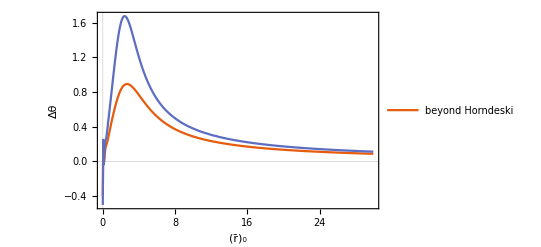

```mathematica
A=ListPlot[{DatosA,BH},PlotTheme->{"Scientific"},BaseStyle->14, FrameLabel->{"(r̄)_0","Δθ"},ImageSize->400,PlotRange->All,PlotLegends->Placed[{"beyond Horndeski"},Automatic],Joined->True]
```

```mathematica
Export["datos_BS_sig0_27.dat",N@DatosA]
```

datos_BS_sig0_27.dat

```mathematica
BH=Import["datos_BH_L3_1_5sig0_35.dat"];
```

### Integración numérica

```mathematica
ClearAll[r0,r];
```

```mathematica
(*nn[r_]:=Sqrt[(1-(2 masa)/(8π r))]
gg[r_]:=Sqrt[(1-(2 masa)/(8π r))^-1]*)
```

```mathematica
i[r_]:=(gg[r]/r √((r^2/r0^2 NN[r0]^2/NN[r]^2-1)^-1))
```

```mathematica
Analit[r0_]:=π(√(1/(1-(8Masa)/(8π π r0)))-1); (* paper*)
```

```mathematica
(*angul[r_,r0_]:=Piecewise[{{(gg[r]/r √((r^2/r0^2 NN[r0]^2/NN[r]^2-1)^-1))^2,r≤rlim},{(Sqrt[(1-(2 Masa)/(8π r))^-1]/r √((r^2/r0^2(1-(2 Masa)/(8π r0))/(1-(2 Masa)/(8π r))-1)^-1)),r>rlim}}];*)
```

```mathematica
Datos={} (* la integral es integrando hasta una r0 sucesivamente y se guarda en Datos*);

For[r0=.5,r0<20,r0+=0.05,

If[r0>rlim,
alpha=2(NIntegrate[(Sqrt[(1-(2 Masa)/(8π r))^-1]/r √((r^2/r0^2(1-(2 Masa)/(8π r0))/(1-(2 Masa)/(8π r))-1)^-1)),{r,r0,Infinity}])-π,
alpha=Last[2(NIntegrate[Evaluate[i[r]/.s1],{r,r0,rlim}]+NIntegrate[(Sqrt[(1-(2 Masa)/(8π r))^-1]/r √((r^2/r0^2(1-(2 Masa)/(8π r0))/(1-(2 Masa)/(8π r))-1)^-1)),{r,rlim,Infinity}])-π]
];
AppendTo[Datos,{r0,alpha}]
]
```

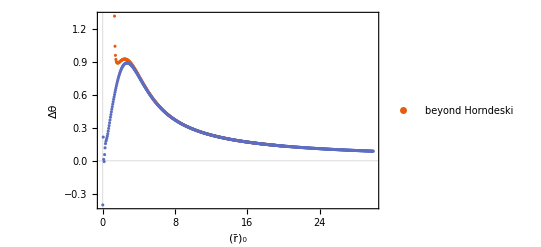

```mathematica
ListPlot[{Datos,DatosA},PlotTheme->{"Scientific"},BaseStyle->14, FrameLabel->{"(r̄)_0","Δθ"},ImageSize->400,PlotRange->All,PlotLegends->Placed[{"beyond Horndeski"},Automatic],Joined->False]
```

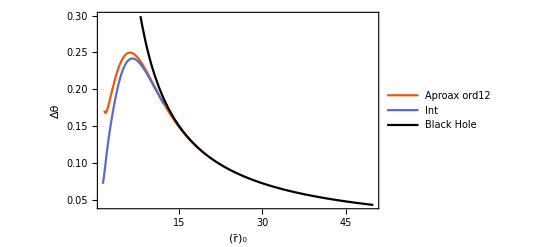

```mathematica
Show[{ListPlot[{Datos,DatosA[[5;;]]},PlotTheme->{"Scientific"},BaseStyle->14, FrameLabel->{"(r̄)_0","Δθ"},ImageSize->400,PlotRange->All,PlotLegends->Placed[{"Aproax ord12", "Int"},Automatic],Joined->True],Plot[Analit[x],{x,8,50},PlotStyle->Black,PlotRange->All,PlotLegends->Placed[{"Black Hole"},Automatic]]},
PlotRange->All(*{{12,rMax+10},{0.05,0.23}}*)
]
```

### Datos

### ISCO

```mathematica
isco[r_]:=NN[r]-r NN'[r]
```

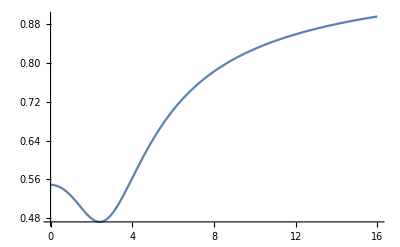

```mathematica
Plot[Evaluate[isco[r]/.s1],{r,rMin,rMax}]
```

```mathematica
Evaluate[isco[r]/.s1]
```

{InterpolatingFunction[…][r]-r InterpolatingFunction[…][r]}

```mathematica
FindRoot[isco[r]==0,{r,0.1,10}]
```

InterpolatingFunction::dmval: Input value {-10.9} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-1.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{r→0.0999287}

```mathematica
isco[r_]:=Evaluate[NN[r]-r NN'[r]/.s1]
```

```mathematica
Last[FindRoot[isco[r]==0,{r,rMin+0.5,rMax}]];
```

InterpolatingFunction::dmval: Input value {-14.5} lies outside the range of data in the interpolating function. Extrapolation will be used.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

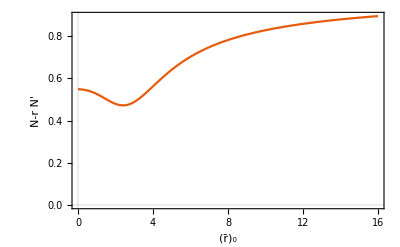

```mathematica
Plot[isco[r],{r,rMin,rMax},AxesOrigin->{0,0},PlotTheme->"Scientific",FrameLabel->{"(r̄)_0","N-r N'"},ImageSize->400]
```